{c→25.9907,k→0.354952,b→11.8615}

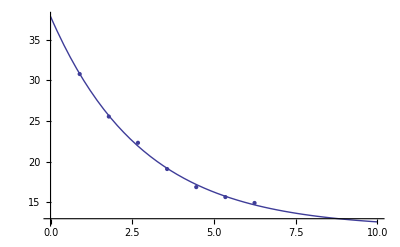

```mathematica
data = {
{0.8914285714,30.7763428571},
{1.7828571428,25.5526857143},
{2.6742857142,22.3290285714},
{3.5657142856,19.1053714285},
{4.457142857,16.8817142857},
{5.3485714284,15.6580571428},
{6.2399999998,14.9343999999}
};
model = c*Exp[-k*x]+b;
fit = FindFit[data,model,{c,k,b},x,MaxIterations->100000]
ffit = model/. fit;
plot = Plot[ffit, {x,0,10}];
pdata = ListPlot[data];
Show[plot,pdata]
```